```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=Read[StringToStream[input[[2]]]];
tmax=Read[StringToStream[input[[4]]]];
nStore=Read[StringToStream[input[[6]]]];
nTrajectory=Read[StringToStream[input[[8]]]];
nBin=Read[StringToStream[input[[10]]]];
yWall=Read[StringToStream[input[[12]]]];
lambda=Read[StringToStream[input[[14]]]];
deltaZ=Read[StringToStream[input[[16]]]];
deltaPz=Read[StringToStream[input[[18]]]];
transitTime=Read[StringToStream[input[[20]]]];
density=Read[StringToStream[input[[22]]]];
rabi=Read[StringToStream[input[[24]]]];
kappa=Read[StringToStream[input[[26]]]];
invT2 = Read[StringToStream[input[[28]]]];
controlType = input[[30]];
name =input[[32]]
```

pois_dt0.005_dZ0_dPz0_tau1.0_nBin50_dens100_g3_k90_yWall1.0

```mathematica
(*Define steady states*)
```

```mathematica
steadyMultiplier = 10;
t0=steadyMultiplier*transitTime;
n0=Ceiling[t0/tmax*nStore];
gc=rabi^2/kappa;
```

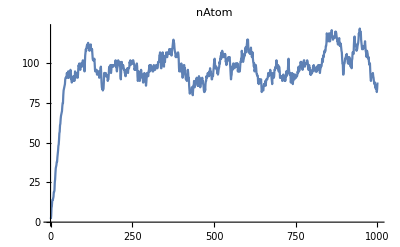

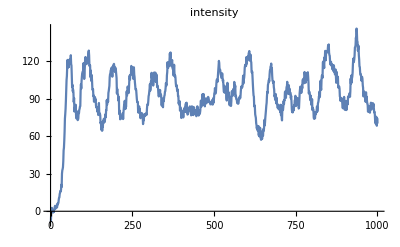

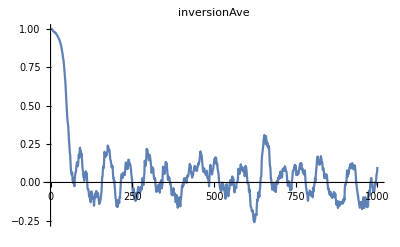

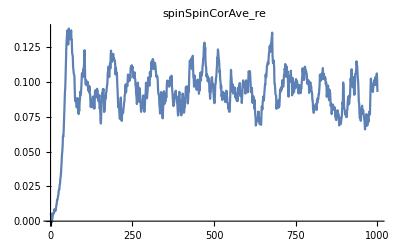

ListLinePlot[Flatten[$Failed],PlotRange→All,PlotLabel→spinSpinCorAve_im]

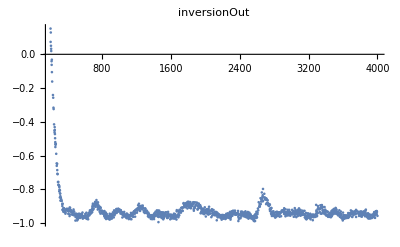

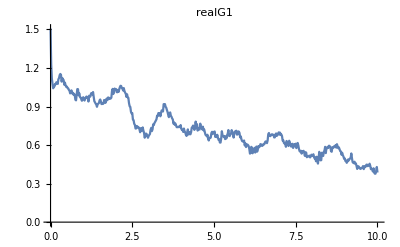

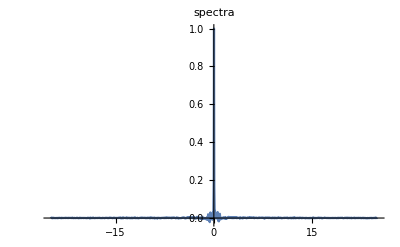

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>controlType <>"/"<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/inversionAve.dat"]];
spinSpinCorAveRe=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCorAve_re.dat"]];
spinSpinCorAveIm=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCorAve_im.dat"]];
spinSpinCorRe=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCor_re.dat"]];
spinSpinCorIm=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCor_im.dat"]];
szMatrix=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/szMatrix.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListLinePlot[inversionAve,PlotRange->All,PlotLabel->"inversionAve"]
ListLinePlot[spinSpinCorAveRe,PlotRange->All,PlotLabel->"spinSpinCorAve_re"]
ListLinePlot[spinSpinCorAveIm,PlotRange->All,PlotLabel->"spinSpinCorAve_im"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversionOut"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

```mathematica
(*Getting steady-state values*)
nAtomSS=Mean[Take[nAtom,-(nStore-n0+1)]]
intensitySS=Mean[Take[intensity,-(nStore-n0+1)]]
inversionAveSS=Mean[Take[inversionAve,-(nStore-n0+1)]]
inversionSumSS =nAtomSS*inversionAveSS
```

31929/317

97.0246

0.0073077

0.736049

FittedModel[0.00190875/(0.000826632+4 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth | 0.0287512 | 0.0309519 | 0.928899 | 0.355201
A | 0.0663886 | 0.0364935 | 1.81919 | 0.0719052

0.0287512

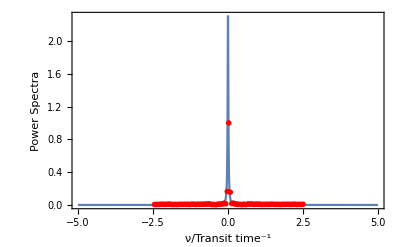

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A linewidth/(linewidth^2+4x^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
linewidth1 = linewidth/.fitLoren["BestFitParameters"]
Show[{Plot[fitLoren[x],{x,-5,5},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.01],Map[Point,spectra]}]},Frame->True,FrameLabel->{"ν/Transit time^-1","Power Spectra"}]
```

```mathematica
tauc1=1/(linewidth1 Pi)
```

11.0712

```mathematica
(*Fit the G1 function to exponential*)
c1=-kappa/2;
c2=-rabi/2;
c3=-rabi/2*inversionSumSS;
c4=0;
```

```mathematica
s1=inversionSumSS/2*gc
s2=-kappa/2-inversionSumSS/2*gc;
```

0.0368024

```mathematica
(*A1=((s1-c4)A0+c2 B0)/(s1-s2);
A2=((c4-s2)A0-c2 B0)/(s1-s2)*)
```

A1 ⅇ^(-A2 t)

FittedModel[1.09329 ⅇ^(-0.0891779 t)]

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 1.09329 | 0.0069849 | 156.521 | 0.
A2 | 0.0891779 | 0.00142822 | 62.4397 | 5.88245×10^-238

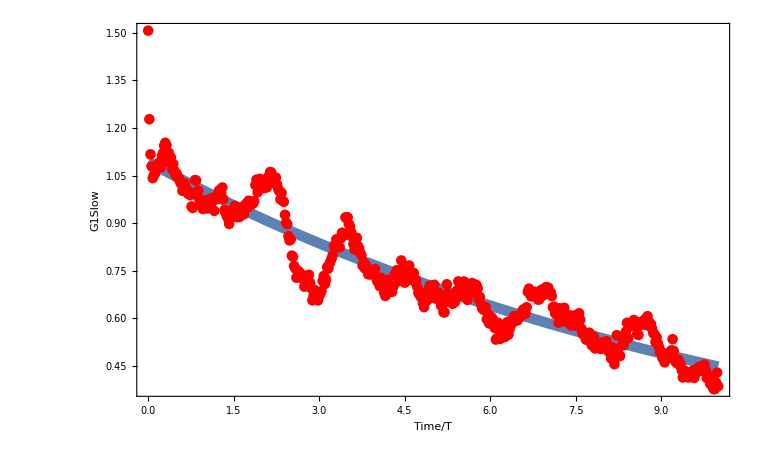

```mathematica
exponentialModel=A1 Exp[-A2 t]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{A1,A2},{t}]
fitExp["ParameterTable"]
(*tauc2=-A2/.fitExp["BestFitParameters"]*)
Show[{Plot[fitExp[x],{x,0,Last[realG1][[1]]},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.01],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1Slow"}]
```

```mathematica
(*Get the linewidth from the coherent time*)
linewidth2 = A2./
```

A2

```mathematica
(*Notice there is another exponential decay.*)
```

```mathematica
(*cutOff = 0.06;
ListPlot[realG1,PlotRange->{{0,cutOff},{0,3}}, 
PlotLabel->"realG1",PlotMarkers->{Automatic,Small}]
secondNum=IntegerPart[cutOff/realG1[[2,1]]];
secondExp=Take[realG1,secondNum];
exponentialModel2=B2 Exp[- Pi linewidthQuick t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{linewidthQuick,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,cutOff},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.02],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1Fast"}]*)
```